```mathematica
c={0,0,0,0};
cmin={-2,-2,-2,-2};
cmax={2,2,2,2};
epsR[p_,f_,fp_,xi_,xf_]:=(NIntegrate[Abs[(fp[x]-f[x])/f[x]]^p,{x,xi,xf},Method->{"GlobalAdaptive",Method->{"GaussKronrodRule","Points"->15}},MaxRecursion->14,WorkingPrecision->10])^(1/p);
```

```mathematica
monteCarlo[]:=
Block[{},
	Do[
		c[[it]]=RandomReal[{cmin[[it]],cmax[[it]]}];
	,{it,Length[c]}]
];
```

```mathematica
gradientDescent[p_,rate_,maxN_]:=
Block[{gradient={},epsilon=10^-2,csafe=c,y1,y2},
	Do[AppendTo[gradient,0],{it,Length[c]}];
	Do[
		Do[
			y1=epsR[p,b1,besselK1,0,100];
			Print[y1];
			csafe[[it]]=c[[it]];
			c[[it]]*(1+epsilon);
			y2=epsR[p,b1,besselK1,0,100];
			gradient[[it]]=(y2-y1)/epsilon;
			c[[it]]=csafe[[it]];
		,{it,Length[c]}];
		Do[c[[it]]-=rate*gradient[[it]],{it,Length[c]}];
	,{jt,maxN}]
];
```

```mathematica
optimizer[p_,N_]:=
Block[{epsmin=10^6,epsnow,copt={}},
	Do[AppendTo[copt,0],{it,Length[c]}];
	Do[
		monteCarlo[];
		epsnow=epsR[p,b1,besselK1,0,100];
		If[epsnow< epsmin,Do[copt[[it]]=c[[it]],{it,Length[c]}];epsmin=epsnow;Print[epsnow];Print[copt]];
	,{it,N}];
	c=copt;
];
```

```mathematica
c0=1.984;
```

```mathematica
besselK1[x_]:=Exp[-x]*(1+1/x)/(c[[1]]*x^(c0/5)+c[[2]]*x^(c0/4)+c[[3]]*x^(c0/3)+c[[4]]*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0));
besselK2[x_]:=Exp[-x]*(1+2.627/x+2/x^2)/(0.033*x^(c0/5)-0.102*x^(c0/4)+0.113*x^(c0/3)+1.162*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2c0));
b1[x_]:=BesselK[1,x];
b2[x_]:=BesselK[2,x];
```

```mathematica
c[[1]]=0.5977191450298387;
c[[2]]=-1.574589670235007;
c[[3]]=0.900841509331037;
c[[4]]=0.8933154980535225;
```

```mathematica
epsR[2,b1,besselK1,0,100]
```

0.3492109817

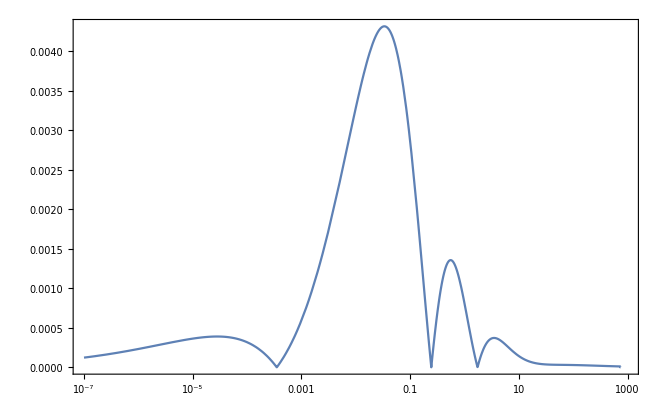

```mathematica
LogLinearPlot[{Abs[besselK1[x]/BesselK[1,x]-1]},{x,10^-7,1000},PlotTheme->"FrameGrid"]
```

```mathematica
epsR[3,b1,besselK1,0,100]
```

0.03438616181

```mathematica
gradientDescent[3,0.01,10]
```

```mathematica
BesselK[1,0.00001]
```

100000.

```mathematica
c[[0]]=1.42286;
c[[1]]=-1.22775;
c[[2]]=0.913203;
c[[3]]=1.27631;
```

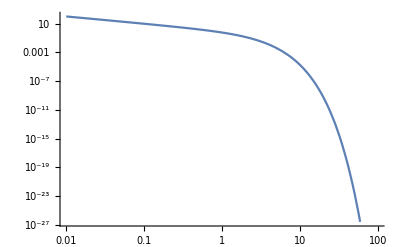

```mathematica
LogLogPlot[besselK1[x],{x,0.01,100}]
```

```mathematica
besselK1[1]
```

0.864381-0.875401 ⅈ

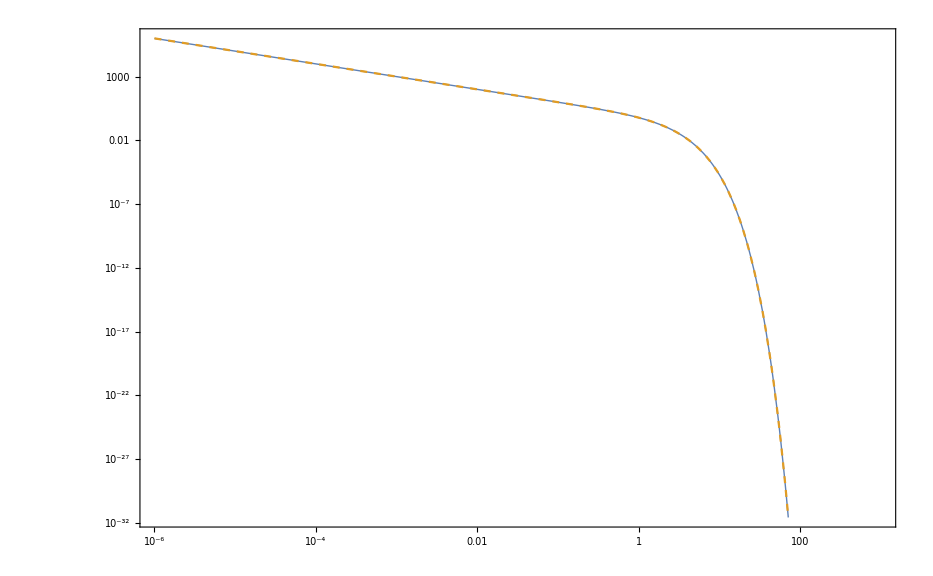

```mathematica
LogLogPlot[{besselK1[x],BesselK[1,x]},{x,10^-6,1000},PlotTheme->"FrameGrid",PlotStyle->{Thick,Dashed}]
```

```mathematica
Clear[c0]
```

```mathematica
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c0]//FullSimplify
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c1]
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c2]
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c3]
D[Exp[-x]*(1+1/x)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c4]
```

1/(2 c0^2)ⅇ^-x (1+1/x) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1/2/c0) (-(c0 ((12 c1 x^(c0/5)+15 c2 x^(c0/4)+20 c3 x^(c0/3)+30 c4 x^(c0/2)) Log[x]+15 2^(2+c0) π^-c0 x^c0 Log[(2 x)/π]))/(60 (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0))+Log[1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0])

-(ⅇ^-x (1+1/x) x^(c0/5) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

-(ⅇ^-x (1+1/x) x^(c0/4) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

-(ⅇ^-x (1+1/x) x^(c0/3) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

-(ⅇ^-x (1+1/x) x^(c0/2) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

```mathematica
15*2^(2+c0) π^-c0 x^c0 Log[(2 x)/π]
```

15 2^(2+c0) π^-c0 x^c0 Log[(2 x)/π]

```mathematica
2^(2+c0)//Simplify
```

2^(2+c0)

```mathematica
2^2*2^c0
```

2^(2+c0)

```mathematica
D[Abs[x^3],x]//Simplify
```

3 Abs[x]^2 Abs'[x]

```mathematica
D[Abs[a*x^2/f(x)-1],a]
```

(x^3 Abs'[-1+(a x^3)/f])/f